# CantorDust

Create a multi-dimensional Cantor set region

## Definition

```mathematica
ClearAll[cantor,CantorRegion,CantorDust]
cantor={a_,b_}:>{{a,a+(b-a)/3},{a+(b-a)2/3,b}};
CantorRegion[n_Integer?NonNegative]:=
Module[{ints},
ints=Nest[Flatten[Map[Function[s,s/.cantor],#],1]&,{{0,1}},n];
MeshRegion[Transpose[{Flatten[ints]}],Line@Table[{i,i+1},{i,1,Length[ints]2,2}],MeshCellStyle->{{0,_}->Directive[Black,PointSize[Medium]],{1,_}->Directive[Thick,Orange]}]]
CantorDust[k_,n_,options:OptionsPattern[Region]]:=Region[RegionProduct@@Table[CantorRegion[k],{n}],options]
```

## Documentation

### Usage

CantorDust[iteration, dimension]

create Cantor dust by deleting elements up to iteration in dimension.

### Details & Options

The dimension can be 1, 2, or 3.

This example is from the documentation for Region Product.

## Examples

### Basic Examples

Create cantor dust in 1 dimension:

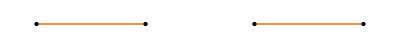
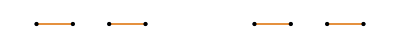
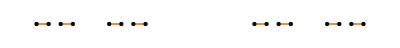
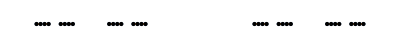
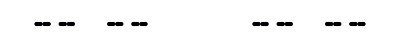
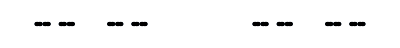

```mathematica
Table[CantorDust[k,1],{k,6}]
```

Create cantor dust in 2 dimensions:

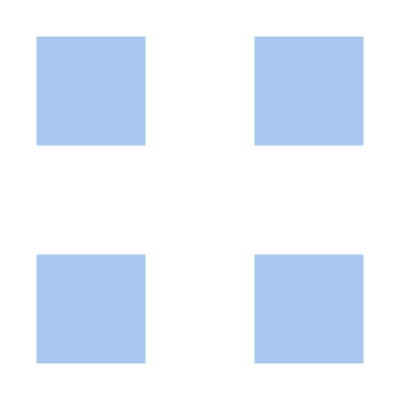
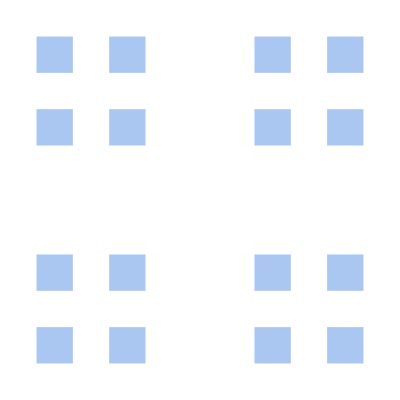
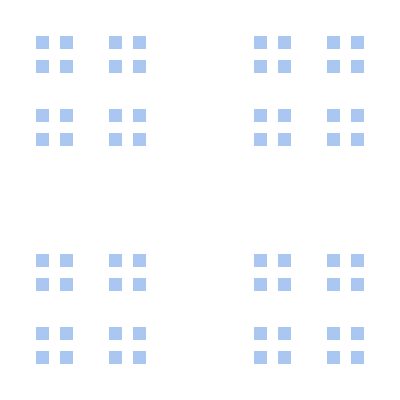
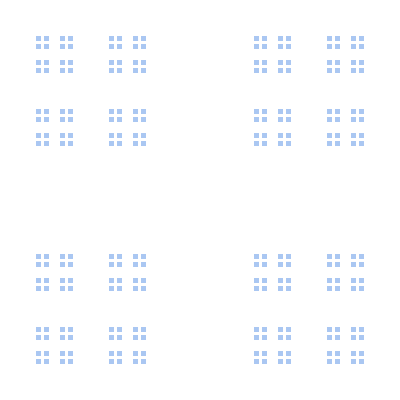
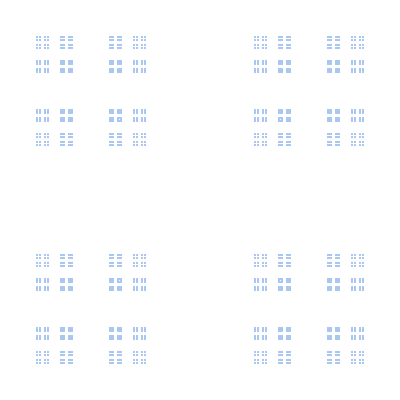
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[CantorDust[k,2],{k,6}]
```

Create Cantor dust in three dimensions:

```mathematica
Table[CantorDust[k,3],{k,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

Make a large image of Cantor dust in 2D:

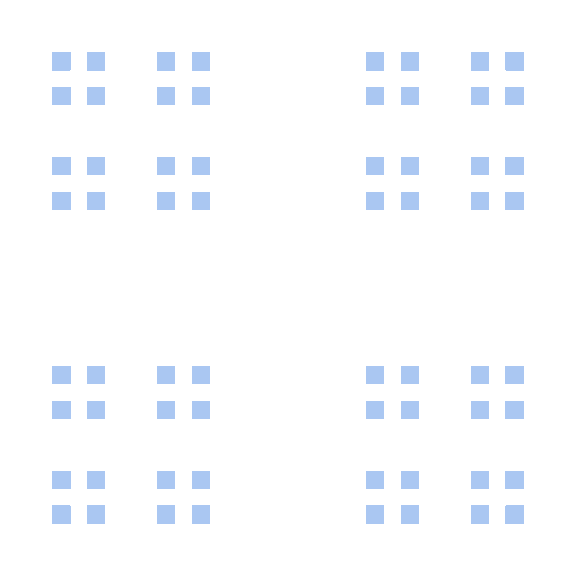

```mathematica
CantorDust[3,2,ImageSize->Large]
```

In 3D:

```mathematica
CantorDust[3,3,ImageSize->Large]
```

-Graphics3D-

Make a very detail image in 2D:

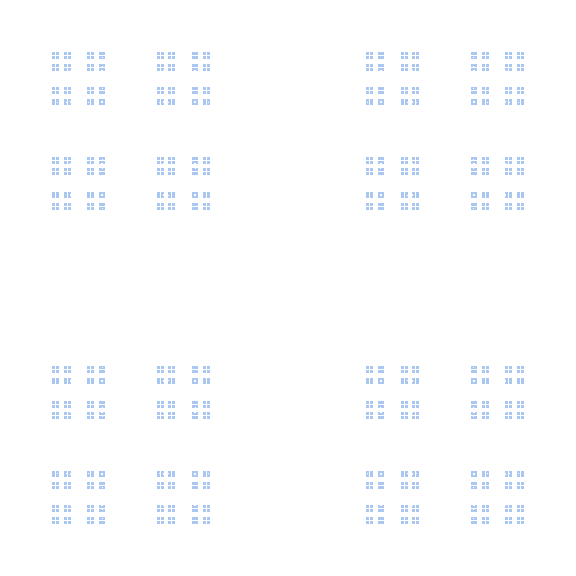

```mathematica
CantorDust[6,2,ImageSize->Large]
```

In 3D:

```mathematica
CantorDust[6,3,ImageSize->Large]
```

-Graphics3D-

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

Find the area of 2D Cantor dust:

```mathematica
Table[RegionMeasure[CantorDust[n,2]],{n,9}]
```

{0.444444,0.197531,0.0877915,0.0390184,0.0173415,0.00770735,0.00342549,0.00152244,0.000676639}

Find the volume of 3D Cantor dust:

```mathematica
Table[RegionMeasure[CantorDust[n,3]],{n,6}]
```

{0.296296,0.0877915,0.0260123,0.00770735,0.00228366,0.000676639}

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Cantor set

Cantor dust

fractals

geometry

set theory

topology

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

RegionProduct

RegionUnion

Region

RegionSymmetricDifference

### Related Resource Objects

KleinBottleGraph

SimplexBoundary

PersistentHomology

SimplexMeasure

### Source/Reference Citation

Wikipedia—Cantor set

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.